```mathematica
import=filename↦Import[
filename,
Path->NotebookDirectory[]<>"/data-source/csse_covid_19_data/csse_covid_19_time_series"
];
confirmed=import["time_series_19-covid-Confirmed.csv"];
dead=import["time_series_19-covid-Deaths.csv"];
recovered=import["time_series_19-covid-Recovered.csv"];
stripNonValues=#[[5;;]]&;
header=confirmed[[1]];
parseShittyDate=fuckoff↦DateObject[
Map[
ToExpression,
Part[StringSplit[fuckoff,"/"],{3,1,2}]
]/.{y_,m_,d_}->{y+2000,m,d}
];
daysSince2020=Map[Composition[(#-t2020)/(60 60 24)&,UnixTime,parseShittyDate],stripNonValues[header]];
onlyGerman=data↦Select[data,#[[2]]=="Germany"&][[1]];
germanConfirmed=stripNonValues[onlyGerman[confirmed]];
germanDead=stripNonValues[onlyGerman[dead]];
germanRecovered=stripNonValues[onlyGerman[recovered]];
```

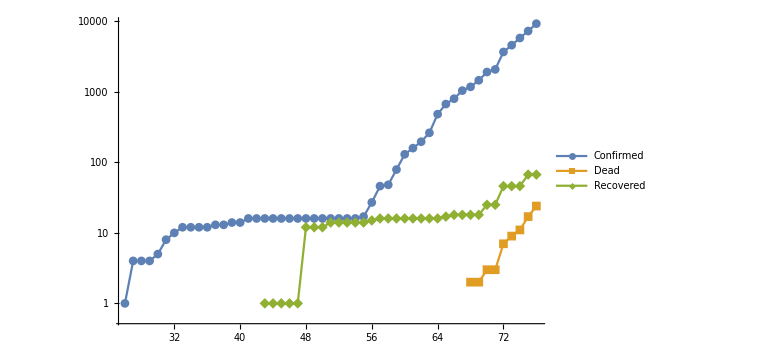

```mathematica
timeSeries=data↦Transpose[{daysSince2020,data}];
ListLogPlot[
timeSeries/@{germanConfirmed,germanDead,germanRecovered},
Joined->True,
PlotMarkers->Automatic,
PlotLegends->{"Confirmed","Dead","Recovered"},
ImageSize->Large
]
```

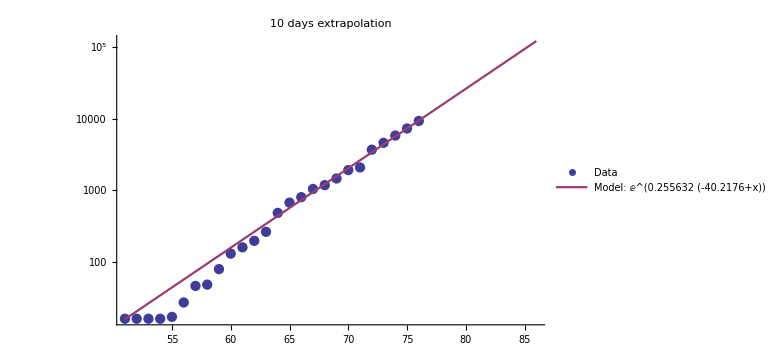
Doubling every 2.7 days
 | Estimate | Standard Error | t-Statistic | P-Value
a | 0.255632 | 0.00526157 | 48.5848 | 1.75042×10^-25
x0 | 40.2176 | 0.706776 | 56.9029 | 4.07018×10^-27
-Graphics-

```mathematica
logExtrapolation={dataInput,startDayString,daysToExtrapolate}↦Module[
{data=dataInput,nlm,timeCoordinates,mmaColors,dataPlot,modelPlot},

startDay=DateValue[startDayString,"ISOYearDay"];

data=Select[data,#/.{t_,_}->t≥startDay&];
nlm=NonlinearModelFit[data,Exp[a (x-x0)],{{a,0.3},{x0,40}},x];
timeCoordinates=Map[#/.{t_,_}->t&,data];
{from,to}={Min[timeCoordinates],Max[timeCoordinates]};

mmaColors=ColorData[1,"ColorList"];
dataPlot=ListLogPlot[data,PlotRange->All,PlotStyle->mmaColors[[1]],PlotLegends->{"Data"}];
modelPlot=LogPlot[nlm[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[2]],PlotLegends->{Row@{"Model: ",Normal[nlm]}}];
Column@{
"Doubling every "<>ToString[Round[Log[2]/(a/.nlm["BestFitParameters"]),0.1]]<>" days",
nlm["ParameterTable"],
Show[dataPlot, modelPlot,PlotRange->All,ImageSize->Large,PlotLabel->ToString[daysToExtrapolate]<>" days extrapolation"]
}
];
logExtrapolation[timeSeries[germanConfirmed],"2020-02-20",10]
```

```mathematica
DateString[
```